```mathematica
α=2.;u0=1.*10^-8;r1=50.;r2=u0;
V[r_]=(*-1/r-(1.0415223038416566 ⅇ^(-0.9990999998788636 r))/r;*)-1/r;(*Which[r>r1,0,True,-1];*)
k=√(2e);l=0;
```

```mathematica
e=0.003;
FindRoot[-2k NIntegrate[V[r] r^2 SphericalBesselJ[0,k r]^2,{r,0,5000}]==E^(I δ)Sin[δ],{δ,-π,π},AccuracyGoal->20,MaxIterations->10000]
-2k NIntegrate[V[r] r^2 SphericalBesselJ[0,k r]^2,{r,0,50}]-E^(I δ)Sin[δ]/.%
```

{δ→44.765-2.61458 ⅈ}

-61.0244+5.68434×10^-14 ⅈ

```mathematica
ⅇ^(ⅈ δ)Sin[δ]==-(2 m k)/ℏ^2∫_0^∞ V[r] SphericalBesselJ[l,k r]^2 r^2 ⅆr
```

```mathematica
NIntegrate[V[r]SphericalBesselJ[l,k r]SphericalBesselY[l,k r] r^2,{r,0,∞}]
```

NIntegrate::inumr: 在以 {{∞,0.}} 为界的区域内，对于所有采样点，计算被积函数 -r SphericalBesselJ[0,√2 √e r] SphericalBesselY[0,√2 √e r] 得到非数值.

NIntegrate[V[r] SphericalBesselJ[l,k r] SphericalBesselY[l,k r] r^2,{r,0,∞}]

```mathematica
ⅇ^(ⅈ δ)Sin[δ]==RealConstant
```

```mathematica
∫_0^∞ V[r]SphericalBesselJ[l,k r]SphericalBesselY[l,k r] r^2 ⅆr
```

∫_0^∞ SphericalBesselJ[l,0.0774597 r] SphericalBesselY[l,0.0774597 r]ⅆr

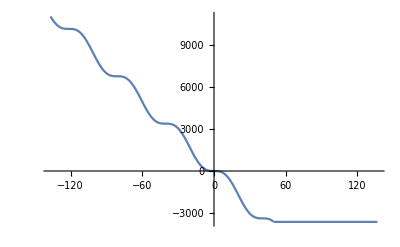

```mathematica
Plot[Piecewise[{{-166.66666666666666 (0.5 r-3.227486121839514 Sin[0.15491933384829668 r]),r≤50.}},-3631.88724784465],{r,-136.8825303141094,136.8825303141094}]
```

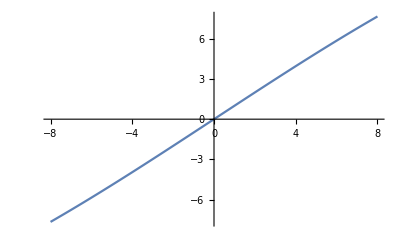

```mathematica
Plot[1/r 166.6666666666666 (-0.5+0.5 Cos[0.1549193338482967 r]+0.07745966692414835 r SinIntegral[0.1549193338482967 r]),{r,-8,8}]
```

```mathematica
FunctionExpand[SphericalBesselJ[0,kr]]
```

Sin[kr]/kr

```mathematica
Unset[e];
```